## Discrete data: blood test example

We first import the data file  “bloodtype.dat”, which contains the blood group and sex of a list of patients.

```mathematica
nb = NotebookDirectory[];
```

```mathematica
SetDirectory[nb]
```

D:\University_of_Aberdeen\Semester_2\PX5510_Statistics_and_Time_Series_Analysis\Notebooks

```mathematica
FileNames["bloodtype.dat"]
```

{bloodtype.dat}

```mathematica
bloodtypelist = Import["bloodtype.dat"];
```

```mathematica
Dimensions[bloodtypelist]
```

{573,3}

That means, we have a matrix of 573 rows and 3 columns.
Now we display the matrix in table form as follows:

```mathematica
bloodtypelist //TableForm
```

Patient | Bloodgroup | Sex
1 | A | f
2 | A | f
3 | A | f
4 | A | f
5 | A | f
6 | A | f
7 | A | f
8 | A | f
9 | A | f
10 | A | f
11 | A | f
12 | A | f
13 | A | f
14 | A | f
15 | A | f
16 | A | f
17 | A | f
18 | A | f
19 | A | f
20 | A | f
21 | A | f
22 | A | f
23 | A | f
24 | A | f
25 | A | f
26 | A | f
27 | A | f
28 | A | f
29 | A | f
30 | A | f
31 | A | f
32 | A | f
33 | A | f
34 | A | f
35 | A | f
36 | A | f
37 | A | f
38 | A | f
39 | A | f
40 | A | f
41 | A | f
42 | A | f
43 | A | f
44 | A | f
45 | A | f
46 | A | f
47 | A | f
48 | A | f
49 | A | f
50 | A | f
51 | A | f
52 | A | f
53 | A | f
54 | A | f
55 | A | f
56 | A | f
57 | A | f
58 | A | f
59 | A | f
60 | A | f
61 | A | f
62 | A | f
63 | A | f
64 | A | f
65 | A | f
66 | A | f
67 | A | f
68 | A | f
69 | A | f
70 | A | f
71 | A | f
72 | A | f
73 | A | f
74 | A | f
75 | A | f
76 | A | f
77 | A | f
78 | A | f
79 | A | f
80 | A | f
81 | A | f
82 | A | f
83 | A | f
84 | A | f
85 | A | f
86 | A | f
87 | A | f
88 | A | f
89 | A | f
90 | A | f
91 | A | f
92 | A | f
93 | A | f
94 | A | f
95 | A | f
96 | A | f
97 | A | f
98 | A | f
99 | A | f
100 | A | f
101 | A | f
102 | A | f
103 | A | f
104 | A | f
105 | A | f
106 | A | f
107 | A | f
108 | A | f
109 | A | m
110 | A | m
111 | A | m
112 | A | m
113 | A | m
114 | A | m
115 | A | m
116 | A | m
117 | A | m
118 | A | m
119 | A | m
120 | A | m
121 | A | m
122 | A | m
123 | A | m
124 | A | m
125 | A | m
126 | A | m
127 | A | m
128 | A | m
129 | A | m
130 | A | m
131 | A | m
132 | A | m
133 | A | m
134 | A | m
135 | A | m
136 | A | m
137 | A | m
138 | A | m
139 | A | m
140 | A | m
141 | A | m
142 | A | m
143 | A | m
144 | A | m
145 | A | m
146 | A | m
147 | A | m
148 | A | m
149 | A | m
150 | A | m
151 | A | m
152 | A | m
153 | A | m
154 | A | m
155 | A | m
156 | A | m
157 | A | m
158 | A | m
159 | A | m
160 | A | m
161 | A | m
162 | A | m
163 | A | m
164 | A | m
165 | A | m
166 | A | m
167 | A | m
168 | A | m
169 | A | m
170 | A | m
171 | A | m
172 | A | m
173 | A | m
174 | A | m
175 | A | m
176 | A | m
177 | A | m
178 | A | m
179 | A | m
180 | A | m
181 | A | m
182 | A | m
183 | A | m
184 | A | m
185 | A | m
186 | A | m
187 | A | m
188 | A | m
189 | A | m
190 | A | m
191 | A | m
192 | A | m
193 | A | m
194 | A | m
195 | A | m
196 | A | m
197 | A | m
198 | A | m
199 | A | m
200 | A | m
201 | A | m
202 | A | m
203 | A | m
204 | A | m
205 | A | m
206 | A | m
207 | A | m
208 | A | m
209 | A | m
210 | A | m
211 | AB | f
212 | AB | f
213 | AB | f
214 | AB | f
215 | AB | f
216 | AB | f
217 | AB | f
218 | AB | f
219 | AB | f
220 | AB | f
221 | AB | f
222 | AB | f
223 | AB | f
224 | AB | f
225 | AB | f
226 | AB | f
227 | AB | f
228 | AB | f
229 | AB | f
230 | AB | f
231 | AB | f
232 | AB | f
233 | AB | f
234 | AB | m
235 | AB | m
236 | AB | m
237 | AB | m
238 | AB | m
239 | AB | m
240 | AB | m
241 | AB | m
242 | AB | m
243 | AB | m
244 | AB | m
245 | AB | m
246 | B | f
247 | B | f
248 | B | f
249 | B | f
250 | B | f
251 | B | f
252 | B | f
253 | B | f
254 | B | f
255 | B | f
256 | B | f
257 | B | f
258 | B | f
259 | B | f
260 | B | f
261 | B | f
262 | B | f
263 | B | f
264 | B | f
265 | B | f
266 | B | f
267 | B | f
268 | B | f
269 | B | f
270 | B | f
271 | B | f
272 | B | f
273 | B | f
274 | B | f
275 | B | f
276 | B | f
277 | B | f
278 | B | f
279 | B | f
280 | B | f
281 | B | f
282 | B | f
283 | B | f
284 | B | f
285 | B | f
286 | B | f
287 | B | f
288 | B | f
289 | B | f
290 | B | f
291 | B | f
292 | B | f
293 | B | m
294 | B | m
295 | B | m
296 | B | m
297 | B | m
298 | B | m
299 | B | m
300 | B | m
301 | B | m
302 | B | m
303 | B | m
304 | B | m
305 | B | m
306 | B | m
307 | B | m
308 | B | m
309 | B | m
310 | B | m
311 | B | m
312 | B | m
313 | B | m
314 | B | m
315 | B | m
316 | B | m
317 | B | m
318 | B | m
319 | B | m
320 | B | m
321 | B | m
322 | B | m
323 | B | m
324 | B | m
325 | B | m
326 | B | m
327 | B | m
328 | B | m
329 | B | m
330 | B | m
331 | B | m
332 | B | m
333 | B | m
334 | B | m
335 | B | m
336 | B | m
337 | B | m
338 | B | m
339 | O | f
340 | O | f
341 | O | f
342 | O | f
343 | O | f
344 | O | f
345 | O | f
346 | O | f
347 | O | f
348 | O | f
349 | O | f
350 | O | f
351 | O | f
352 | O | f
353 | O | f
354 | O | f
355 | O | f
356 | O | f
357 | O | f
358 | O | f
359 | O | f
360 | O | f
361 | O | f
362 | O | f
363 | O | f
364 | O | f
365 | O | f
366 | O | f
367 | O | f
368 | O | f
369 | O | f
370 | O | f
371 | O | f
372 | O | f
373 | O | f
374 | O | f
375 | O | f
376 | O | f
377 | O | f
378 | O | f
379 | O | f
380 | O | f
381 | O | f
382 | O | f
383 | O | f
384 | O | f
385 | O | f
386 | O | f
387 | O | f
388 | O | f
389 | O | f
390 | O | f
391 | O | f
392 | O | f
393 | O | f
394 | O | f
395 | O | f
396 | O | f
397 | O | f
398 | O | f
399 | O | f
400 | O | f
401 | O | f
402 | O | f
403 | O | f
404 | O | f
405 | O | f
406 | O | f
407 | O | f
408 | O | f
409 | O | f
410 | O | f
411 | O | f
412 | O | f
413 | O | f
414 | O | f
415 | O | f
416 | O | f
417 | O | f
418 | O | f
419 | O | f
420 | O | f
421 | O | f
422 | O | f
423 | O | f
424 | O | f
425 | O | f
426 | O | f
427 | O | f
428 | O | f
429 | O | f
430 | O | f
431 | O | f
432 | O | f
433 | O | f
434 | O | f
435 | O | f
436 | O | f
437 | O | f
438 | O | f
439 | O | f
440 | O | f
441 | O | f
442 | O | f
443 | O | f
444 | O | f
445 | O | f
446 | O | f
447 | O | f
448 | O | f
449 | O | f
450 | O | f
451 | O | f
452 | O | f
453 | O | m
454 | O | m
455 | O | m
456 | O | m
457 | O | m
458 | O | m
459 | O | m
460 | O | m
461 | O | m
462 | O | m
463 | O | m
464 | O | m
465 | O | m
466 | O | m
467 | O | m
468 | O | m
469 | O | m
470 | O | m
471 | O | m
472 | O | m
473 | O | m
474 | O | m
475 | O | m
476 | O | m
477 | O | m
478 | O | m
479 | O | m
480 | O | m
481 | O | m
482 | O | m
483 | O | m
484 | O | m
485 | O | m
486 | O | m
487 | O | m
488 | O | m
489 | O | m
490 | O | m
491 | O | m
492 | O | m
493 | O | m
494 | O | m
495 | O | m
496 | O | m
497 | O | m
498 | O | m
499 | O | m
500 | O | m
501 | O | m
502 | O | m
503 | O | m
504 | O | m
505 | O | m
506 | O | m
507 | O | m
508 | O | m
509 | O | m
510 | O | m
511 | O | m
512 | O | m
513 | O | m
514 | O | m
515 | O | m
516 | O | m
517 | O | m
518 | O | m
519 | O | m
520 | O | m
521 | O | m
522 | O | m
523 | O | m
524 | O | m
525 | O | m
526 | O | m
527 | O | m
528 | O | m
529 | O | m
530 | O | m
531 | O | m
532 | O | m
533 | O | m
534 | O | m
535 | O | m
536 | O | m
537 | O | m
538 | O | m
539 | O | m
540 | O | m
541 | O | m
542 | O | m
543 | O | m
544 | O | m
545 | O | m
546 | O | m
547 | O | m
548 | O | m
549 | O | m
550 | O | m
551 | O | m
552 | O | m
553 | O | m
554 | O | m
555 | O | m
556 | O | m
557 | O | m
558 | O | m
559 | O | m
560 | O | m
561 | O | m
562 | O | m
563 | O | m
564 | O | m
565 | O | m
566 | O | m
567 | O | m
568 | O | m
569 | O | m
570 | O | m
571 | O | m
572 | O | m

An alternative way to display the data is using the TableView function:

```mathematica
TableView[bloodtypelist]
```

PatientBloodgroupSex1Af2Af3Af4Af5Af6Af7Af8Af9Af10Af11Af12Af13Af14Af15Af16Af17Af18Af19Af20Af21Af22Af23Af24Af25Af26Af27Af28Af29Af30Af31Af32Af33Af34Af35Af36Af37Af38Af39Af40Af41Af42Af43Af44Af45Af46Af47Af48Af49Af50Af51Af52Af53Af54Af55Af56Af57Af58Af59Af60Af61Af62Af63Af64Af65Af66Af67Af68Af69Af70Af71Af72Af73Af74Af75Af76Af77Af78Af79Af80Af81Af82Af83Af84Af85Af86Af87Af88Af89Af90Af91Af92Af93Af94Af95Af96Af97Af98Af99Af100Af101Af102Af103Af104Af105Af106Af107Af108Af109Am110Am111Am112Am113Am114Am115Am116Am117Am118Am119Am120Am121Am122Am123Am124Am125Am126Am127Am128Am129Am130Am131Am132Am133Am134Am135Am136Am137Am138Am139Am140Am141Am142Am143Am144Am145Am146Am147Am148Am149Am150Am151Am152Am153Am154Am155Am156Am157Am158Am159Am160Am161Am162Am163Am164Am165Am166Am167Am168Am169Am170Am171Am172Am173Am174Am175Am176Am177Am178Am179Am180Am181Am182Am183Am184Am185Am186Am187Am188Am189Am190Am191Am192Am193Am194Am195Am196Am197Am198Am199Am200Am201Am202Am203Am204Am205Am206Am207Am208Am209Am210Am211ABf212ABf213ABf214ABf215ABf216ABf217ABf218ABf219ABf220ABf221ABf222ABf223ABf224ABf225ABf226ABf227ABf228ABf229ABf230ABf231ABf232ABf233ABf234ABm235ABm236ABm237ABm238ABm239ABm240ABm241ABm242ABm243ABm244ABm245ABm246Bf247Bf248Bf249Bf250Bf251Bf252Bf253Bf254Bf255Bf256Bf257Bf258Bf259Bf260Bf261Bf262Bf263Bf264Bf265Bf266Bf267Bf268Bf269Bf270Bf271Bf272Bf273Bf274Bf275Bf276Bf277Bf278Bf279Bf280Bf281Bf282Bf283Bf284Bf285Bf286Bf287Bf288Bf289Bf290Bf291Bf292Bf293Bm294Bm295Bm296Bm297Bm298Bm299Bm300Bm301Bm302Bm303Bm304Bm305Bm306Bm307Bm308Bm309Bm310Bm311Bm312Bm313Bm314Bm315Bm316Bm317Bm318Bm319Bm320Bm321Bm322Bm323Bm324Bm325Bm326Bm327Bm328Bm329Bm330Bm331Bm332Bm333Bm334Bm335Bm336Bm337Bm338Bm339Of340Of341Of342Of343Of344Of345Of346Of347Of348Of349Of350Of351Of352Of353Of354Of355Of356Of357Of358Of359Of360Of361Of362Of363Of364Of365Of366Of367Of368Of369Of370Of371Of372Of373Of374Of375Of376Of377Of378Of379Of380Of381Of382Of383Of384Of385Of386Of387Of388Of389Of390Of391Of392Of393Of394Of395Of396Of397Of398Of399Of400Of401Of402Of403Of404Of405Of406Of407Of408Of409Of410Of411Of412Of413Of414Of415Of416Of417Of418Of419Of420Of421Of422Of423Of424Of425Of426Of427Of428Of429Of430Of431Of432Of433Of434Of435Of436Of437Of438Of439Of440Of441Of442Of443Of444Of445Of446Of447Of448Of449Of450Of451Of452Of453Om454Om455Om456Om457Om458Om459Om460Om461Om462Om463Om464Om465Om466Om467Om468Om469Om470Om471Om472Om473Om474Om475Om476Om477Om478Om479Om480Om481Om482Om483Om484Om485Om486Om487Om488Om489Om490Om491Om492Om493Om494Om495Om496Om497Om498Om499Om500Om501Om502Om503Om504Om505Om506Om507Om508Om509Om510Om511Om512Om513Om514Om515Om516Om517Om518Om519Om520Om521Om522Om523Om524Om525Om526Om527Om528Om529Om530Om531Om532Om533Om534Om535Om536Om537Om538Om539Om540Om541Om542Om543Om544Om545Om546Om547Om548Om549Om550Om551Om552Om553Om554Om555Om556Om557Om558Om559Om560Om561Om562Om563Om564Om565Om566Om567Om568Om569Om570Om571Om572Om

We now build an (absolute) frequency table. Please notice we start from the 2nd row, as the first row contains the name of the column, and we select the second column, which is the one that contains the blood group.

```mathematica
Tally[bloodtypelist[[2;;,2]]]
```

{{A,210},{AB,35},{B,93},{O,234}}

We can also access the absolute frequency of each blood group as follows:

```mathematica
Count[bloodtypelist[[2;;,2]],"AB"]
```

35

```mathematica
Count[bloodtypelist[[2;;,2]],"O"]
```

234

Now we store the absolute frequency table in a variable:

```mathematica
frequBloodtype=Tally[bloodtypelist[[2;;,2]]]
```

{{A,210},{AB,35},{B,93},{O,234}}

We can count the total number of samples in our dataset as follows:

```mathematica
Total[frequBloodtype][[2]]
```

572

```mathematica
Total[frequBloodtype]
```

{A+AB+B+O,572}

We can add names to the columns and create a table to store the absolute frequencies as follows:

```mathematica
Join[{{"Blood Group","frequency"}},frequBloodtype ]//TableForm
```

Blood Group | frequency
A | 210
AB | 35
B | 93
O | 234

We now add a row at the end detailing the total number of samples and store everything in a variable:

```mathematica
BloodTable=Join[{{"Blood Group","frequency"}},Tally[bloodtypelist[[2;;,2]]],{{"total",Total[frequBloodtype][[2]]}} ]
```

{{Blood Group,frequency},{A,210},{AB,35},{B,93},{O,234},{total,572}}

```mathematica
BloodTable //TableForm
```

Blood Group | frequency
A | 210
AB | 35
B | 93
O | 234
total | 572

We now calculate the relative frequency:

```mathematica
relfreq=N[BloodTable[[2;;5,2]] / Total[frequBloodtype][[2]]]
```

{0.367133,0.0611888,0.162587,0.409091}

To add the relative frequency to the table as a column, we first transpose the table, join it with the relative frequency row, and transpose again:

```mathematica
Transpose[BloodTable]
```

{{Blood Group,A,AB,B,O,total},{frequency,210,35,93,234,572}}

```mathematica
Join[Transpose[BloodTable],{Join[{"rel. frequ"}, 
relfreq,{N[Total[BloodTable[[2;;5,2]] / Total[frequBloodtype][[2]]]]}
 ]
}
]
```

{{Blood Group,A,AB,B,O,total},{frequency,210,35,93,234,572},{rel. frequ,0.367133,0.0611888,0.162587,0.409091,1.}}

```mathematica
BloodTable = Transpose[Join[Transpose[BloodTable],{Join[{"rel. frequ"}, BloodTable[[2;;5,2]] / Total[frequBloodtype][[2]],{Total[BloodTable[[2;;5,2]] / Total[frequBloodtype][[2]]]} ]}]]
```

{{Blood Group,frequency,rel. frequ},{A,210,105/286},{AB,35,35/572},{B,93,93/572},{O,234,9/22},{total,572,1}}

```mathematica
BloodTable //TableForm
```

Blood Group | frequency | rel. frequ | rel. frequ
A | 210 | 105/286 | 105/286
AB | 35 | 35/572 | 35/572
B | 93 | 93/572 | 93/572
O | 234 | 9/22 | 9/22
total | 572 | 1 | 1

We can now display the absolute frequencies using a bar chart:

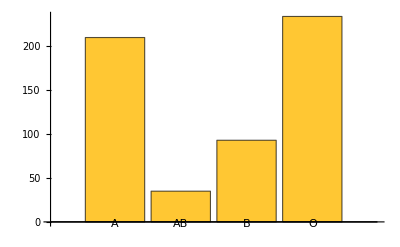

```mathematica
BarChart[BloodTable[[2;;5,2]],ChartLabels->{"A","AB","B","O"}]
```

And we display the relative frequencies as follows:

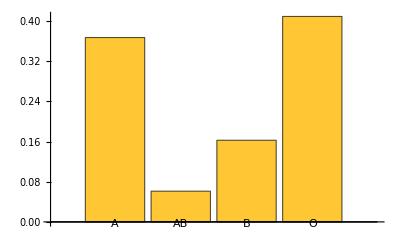

```mathematica
BarChart[BloodTable[[2;;5,3]],ChartLabels->{Transpose[BloodTable][[1,2;;5]]}]
```

We can create a pie chart as follows:

```mathematica
PieChart[BloodTable[[2;;5,3]],ChartLabels->{"A","AB","B","O"}]
```

-Graphics-

We now have a look at the second variable “sex”:

```mathematica
Tally[bloodtypelist[[2;;,2]]]
```

{{A,210},{AB,35},{B,93},{O,234}}

```mathematica
Tally[bloodtypelist[[2;;,3]]]
```

{{f,292},{m,280}}

We can now count samples of different blood groups, distinguishing also according to sex:

```mathematica
Tally[bloodtypelist[[2;;,2;;]]]  //TableForm
```

A
f | 108
A
m | 102
AB
f | 23
AB
m | 12
B
f | 47
B
m | 46
O
f | 114
O
m | 120

Below is a bar chart that plots those absolute frequencies:

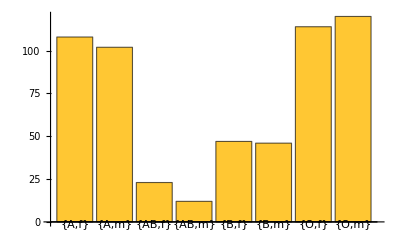

```mathematica
BarChart[Tally[bloodtypelist[[2;;,2;;]]] [[All,2]], ChartLabels->{  Tally[bloodtypelist[[2;;,2;;]]]   [[All,1]] } ]
```

If we want to select only females from the dataset:

```mathematica
Select[bloodtypelist,#[[3]]=="f"&][[All,2]]
```

{A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,A,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,AB,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,B,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O,O}

```mathematica
Tally[%]
```

{{A,108},{AB,23},{B,47},{O,114}}

We now create one list of absolute frequencies for female patients and another one for male patients:

```mathematica
flist=Tally[Select[bloodtypelist,#[[3]]=="f"&][[All,2]]]
```

{{A,108},{AB,23},{B,47},{O,114}}

```mathematica
mlist=Tally[Select[bloodtypelist,#[[3]]=="m"&][[All,2]]]
```

{{A,102},{AB,12},{B,46},{O,120}}

And now we create a paired bar chart:

```mathematica
PairedBarChart[flist[[All,2]],mlist[[All,2]],ChartLabels->{flist[[All,1]] },PlotLabel->"female       male"]
```

-Graphics-

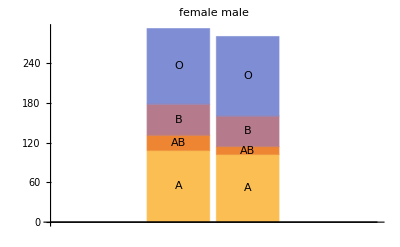

```mathematica
BarChart[{flist[[All,2]],mlist[[All,2]]},ChartLabels->{flist[[All,1]] },ChartLayout->"Stacked",PlotLabel->"female       male"]
```

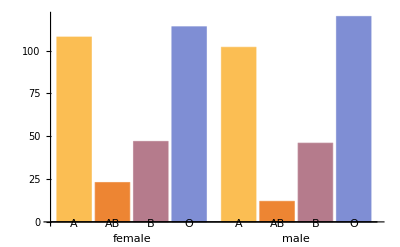

```mathematica
BarChart[{flist[[All,2]],mlist[[All,2]]},ChartLabels->{{"female","male"},{flist[[1,1]],flist[[2,1]],flist[[3,1]],flist[[4,1]] }},ChartLayout->"Grouped"]
```